```mathematica
Predicting Gold Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

## Resources

- PAXG hourly price: Recent (≥ 2020) data - Gemini.

## In This Notebook

LPPLS model implementation (2026 ed.) for Gold price in USD.
Uses PAXG price as a proxy for Gold’s price, due to current lack of access to high quality (hourly) Spot Gold price data.

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-01-29

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Gemini_PAXGUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2020-10-31

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, 0], "ISODate"]==lastPriceDate, lastDownloadedTime=="23:00:00"}
```

{2026-01-29,23:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Convert to seconds *)
hourlyPricesTs={#[[1]]/1000, #[[2]]}&/@closingPricesFilter
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[hourlyPricesTs, First]
```

```mathematica
Length[hourlyPrices]
```

46004

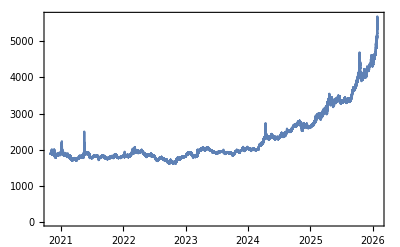

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Gold(PAXG)_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Gold(PAXG)_price-hourly-20201031-20260129.csv

```mathematica
{FromUnixTime[hourlyPrices[[1]][[1]]],FromUnixTime[hourlyPrices[[-1]][[1]]]}
```

{Sat 31 Oct 2020 05:00:00GMT+1,Fri 30 Jan 2026 00:00:00GMT+1}

```mathematica
(* Use the Log Price *)
logPrice= {#[[1]], Log[#[[2]]]}&/@hourlyPrices
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2024-01-01", lastPriceDate}, {"2025-07-01", "2026-01-28"}(* Pre-crash *) }
```

{{2024-01-01,2026-01-29},{2025-07-01,2026-01-28}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1704063600,1769641200},{1751324400,1769554800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{759,211}

```mathematica
bubbles=Table[Select[logPrice,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1704063600,7.61955},{1751324400,8.11043}}

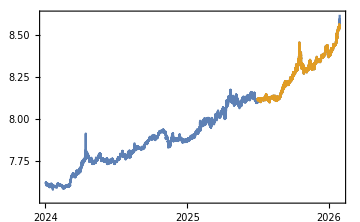

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.,1.},{1.00059,0.992607}}

```mathematica
Length/@bubblesScaled
```

{18217,5065}

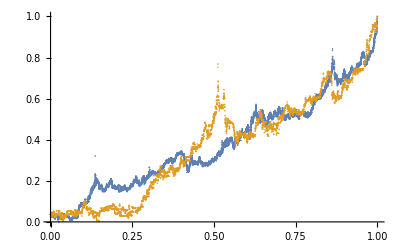

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Gold-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold-1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold-2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.5228,18193.9},{17.5819,5041.86}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{5.25774,0.017,0.000958501},{2.71495,0.0232076,0.00244685}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

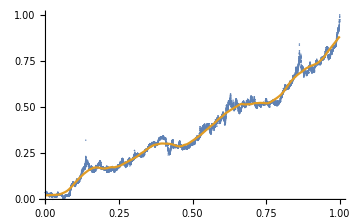
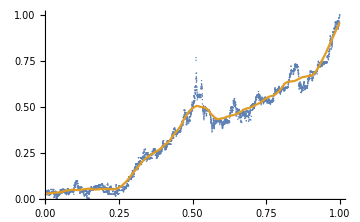

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

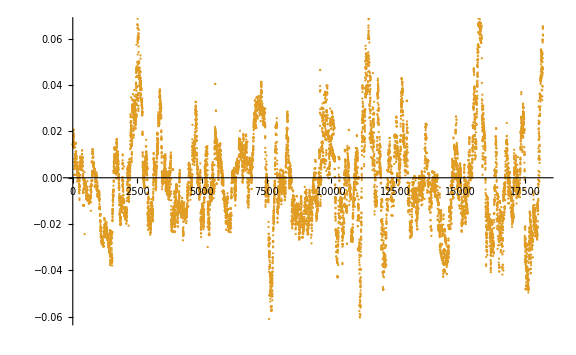
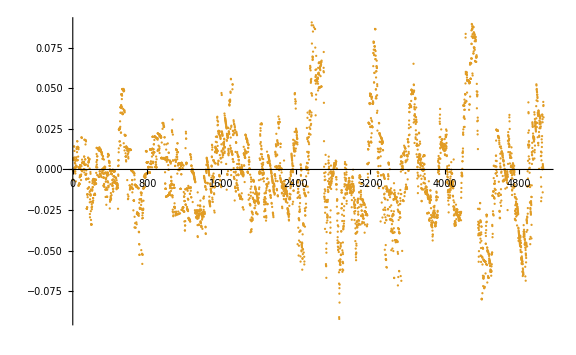

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0203701,0.0300438}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{7.56651,4.5776}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{7.56651 > 5.25774,4.5776 > 2.71495}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.02039,0.0301151}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.02039 > 0.017,0.0301151 > 0.0232076}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0169969,0.0231924}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0203932,0.0301317}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0203932 > 0.017,0.0301317 > 0.0232076}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0169995,0.0232052}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.5819,5041.86}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.00059

2.28495

```mathematica
(* Define 7 days resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.0331754

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0473934

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=
Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Fri 30 Jan 2026 23:47:14GMT+1[]

{4729.44,{{a→0.927707,b→-0.857949,c→-0.00939698,d→0.136429,T_1→0.,tc→1.00069,m→0.6,ω→6.2,RSS→9.48216,ℛerror→0.00187468,ℛσ→0.043272,LL→15628.7,ρ→0.966504,σ→-0.0111048,μ→-1.58189×10^-17},{a→0.926395,b→-0.854057,c→0.00864277,d→0.139868,T_1→0.0473934,tc→1.00069,m→0.6,ω→6.4,RSS→9.26463,ℛerror→0.00192292,ℛσ→0.0438238,LL→14814.5,ρ→0.966324,σ→-0.011276,μ→-1.66089×10^-17},{a→0.924292,b→-0.848932,c→0.0123355,d→0.140617,T_1→0.0947867,tc→1.00069,m→0.6,ω→6.4,RSS→9.1977,ℛerror→0.00200911,ℛσ→0.0447937,LL→14001.1,ρ→0.966702,σ→-0.0114616,μ→9.58743×10^-18},{a→0.925804,b→-0.852695,c→0.00953848,d→0.14068,T_1→0.14218,tc→1.00069,m→0.6,ω→6.4,RSS→9.07448,ℛerror→0.00209186,ℛσ→0.0457052,LL→13269.1,ρ→0.96805,σ→-0.0114596,μ→-2.68746×10^-17},{a→0.927347,b→-0.856757,c→0.00709738,d→0.142444,T_1→0.189573,tc→1.00069,m→0.6,ω→6.4,RSS→9.00254,ℛerror→0.00219681,ℛσ→0.0468359,LL→12464.3,ρ→0.968502,σ→-0.0116609,μ→-2.00454×10^-17},{a→0.926739,b→-0.855447,c→-0.00125254,d→0.140417,T_1→0.236967,tc→1.00069,m→0.6,ω→6.3,RSS→8.85915,ℛerror→0.00229631,ℛσ→0.0478826,LL→11796.7,ρ→0.970639,σ→-0.0115162,μ→-2.46953×10^-17},{a→0.973421,b→-0.84692,c→0.0303405,d→0.107048,T_1→0.28436,tc→1.00069,m→0.5,ω→6.5,RSS→8.05584,ℛerror→0.0022266,ℛσ→0.0471478,LL→11020.3,ρ→0.969255,σ→-0.0115996,μ→2.21567×10^-18},{a→1.02252,b→-0.818371,c→-0.0547292,d→-0.0742719,T_1→0.331754,tc→1.00069,m→0.4,ω→11.6,RSS→6.50791,ℛerror→0.00192656,ℛσ→0.0438536,LL→10283.1,ρ→0.964318,σ→-0.0116084,μ→-6.78543×10^-18},{a→1.01607,b→-0.804403,c→-0.054461,d→-0.0665307,T_1→0.379147,tc→1.00069,m→0.4,ω→11.6,RSS→6.30649,ℛerror→0.00200908,ℛσ→0.0447799,LL→9614.17,ρ→0.967079,σ→-0.0113937,μ→2.81537×10^-17},{a→1.00793,b→-0.786231,c→-0.0465507,d→-0.0605154,T_1→0.42654,tc→1.00069,m→0.4,ω→11.6,RSS→6.06151,ℛerror→0.0020909,ℛσ→0.0456791,LL→8824.51,ρ→0.967075,σ→-0.0116229,μ→4.58619×10^-18},{a→1.00249,b→-0.768726,c→-0.0753493,d→0.0262253,T_1→0.473934,tc→1.00069,m→0.4,ω→5.6,RSS→5.62211,ℛerror→0.00211437,ℛσ→0.0459305,LL→8081.29,ρ→0.967143,σ→-0.0116749,μ→9.9817×10^-18},{a→1.01447,b→-0.798932,c→-0.0588442,d→0.020611,T_1→0.521327,tc→1.00069,m→0.4,ω→5.6,RSS→4.13774,ℛerror→0.00171052,ℛσ→0.0413072,LL→7620.77,ρ→0.966054,σ→-0.0106692,μ→-2.45702×10^-17}}}

```mathematica
(* Shortcut: *)
    fits=
```

```mathematica
(* Timing in hours: *)
fits[[1]]/60/60
```

1.31373

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.00069 | ℛσ→0.043272 | LL→15628.7
T_1→0.0473934 | tc→1.00069 | ℛσ→0.0438238 | LL→14814.5
T_1→0.0947867 | tc→1.00069 | ℛσ→0.0447937 | LL→14001.1
T_1→0.14218 | tc→1.00069 | ℛσ→0.0457052 | LL→13269.1
T_1→0.189573 | tc→1.00069 | ℛσ→0.0468359 | LL→12464.3
T_1→0.236967 | tc→1.00069 | ℛσ→0.0478826 | LL→11796.7
T_1→0.28436 | tc→1.00069 | ℛσ→0.0471478 | LL→11020.3
T_1→0.331754 | tc→1.00069 | ℛσ→0.0438536 | LL→10283.1
T_1→0.379147 | tc→1.00069 | ℛσ→0.0447799 | LL→9614.17
T_1→0.42654 | tc→1.00069 | ℛσ→0.0456791 | LL→8824.51
T_1→0.473934 | tc→1.00069 | ℛσ→0.0459305 | LL→8081.29
T_1→0.521327 | tc→1.00069 | ℛσ→0.0413072 | LL→7620.77

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.00069

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.00069

1.00069

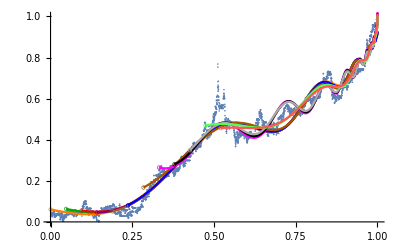

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0473934,0.0947867,0.14218,0.189573,0.236967,0.28436,0.331754,0.379147,0.42654,0.473934,0.521327}

{0.00187468,0.00192292,0.00200911,0.00209186,0.00219681,0.00229631,0.0022266,0.00192656,0.00200908,0.0020909,0.00211437,0.00171052}

{9.48216,9.26463,9.1977,9.07448,9.00254,8.85915,8.05584,6.50791,6.30649,6.06151,5.62211,4.13774}

{0.043272,0.0438238,0.0447937,0.0457052,0.0468359,0.0478826,0.0471478,0.0438536,0.0447799,0.0456791,0.0459305,0.0413072}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

5065

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

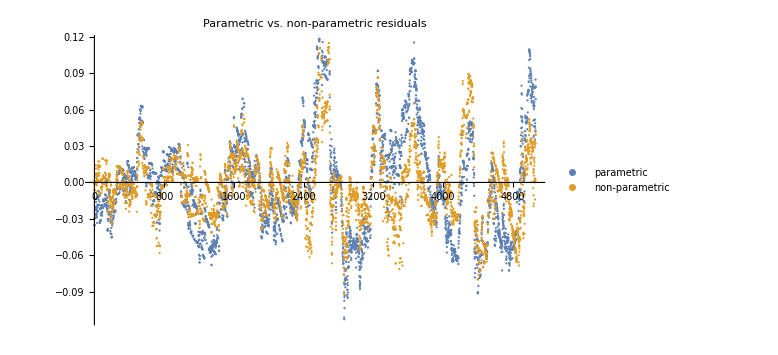

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{4.5776,9.48216}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0301317,0.0432976}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.000907918,0.00187468}

```mathematica
selN=Length[T1s];
selN
```

12

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{5065,4825,4585,4345,4105,3865,3625,3385,3145,2905,2665,2425}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{5065,4825,4585,4345,4105,3865,3625,3385,3145,2905,2665,2425}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-Gold-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{5065,4825,4585,4345,4105,3865,3625,3385,3145,2905,2665,2425}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.00187468,0.00192292,0.00200911,0.00209186,0.00219681,0.00229631,0.0022266,0.00192656,0.00200908,0.0020909,0.00211437,0.00171052}

```mathematica
RSSs
```

{9.48216,9.26463,9.1977,9.07448,9.00254,8.85915,8.05584,6.50791,6.30649,6.06151,5.62211,4.13774}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0300438,0.0306679,0.0313955,0.031728,0.0323882,0.033157,0.0337883,0.034668,0.0355873,0.0367458,0.0380416,0.0351495}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.931049,σ→-0.0109617,μ→-0.000079248},{ρ→0.931766,σ→-0.0111331,μ→-0.0000737807},{ρ→0.932687,σ→-0.0113227,μ→-0.0000692658},{ρ→0.934107,σ→-0.0113254,μ→-0.0000905751},{ρ→0.934575,σ→-0.0115212,μ→-0.000104534},{ρ→0.939495,σ→-0.0113569,μ→-0.000091644},{ρ→0.940343,σ→-0.0114941,μ→-0.0000267973},{ρ→0.942862,σ→-0.0115491,μ→-0.0000590854},{ρ→0.947793,σ→-0.0113465,μ→-0.0000825148},{ρ→0.949077,σ→-0.0115745,μ→-0.0000456866},{ρ→0.951939,σ→-0.0116495,μ→-0.0000351258},{ρ→0.954252,σ→-0.0105076,μ→-0.000135632}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[-0.000079248,{0.931049},0.000120158],ARProcess[-0.0000737807,{0.931766},0.000123946],ARProcess[-0.0000692658,{0.932687},0.000128204],ARProcess[-0.0000905751,{0.934107},0.000128264],ARProcess[-0.000104534,{0.934575},0.000132737],ARProcess[-0.000091644,{0.939495},0.00012898],ARProcess[-0.0000267973,{0.940343},0.000132115],ARProcess[-0.0000590854,{0.942862},0.000133381],ARProcess[-0.0000825148,{0.947793},0.000128744],ARProcess[-0.0000456866,{0.949077},0.000133969],ARProcess[-0.0000351258,{0.951939},0.000135711],ARProcess[-0.000135632,{0.954252},0.000110411]}

{15676.3,14858.6,14042.3,13307.9,12501.2,11829.,11048.,10302.4,9626.5,8834.21,8087.89,7626.35}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

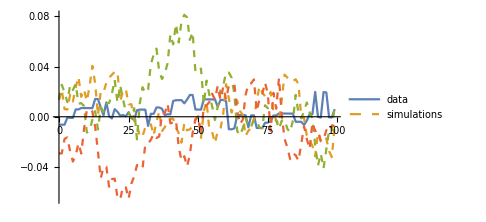
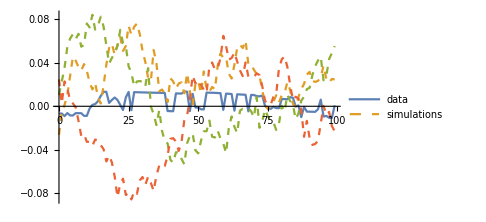
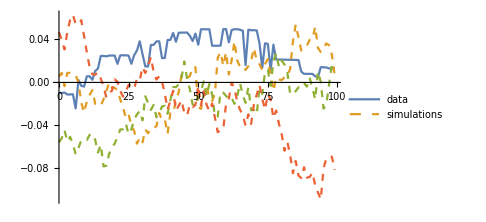
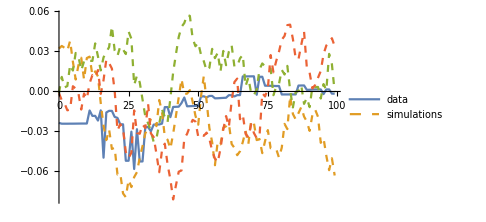
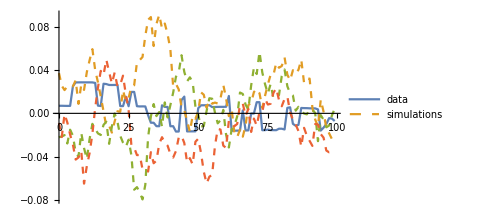
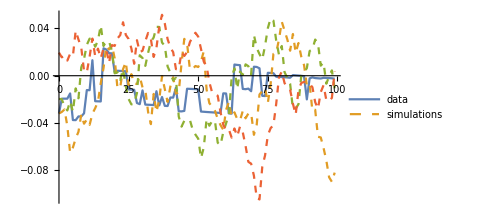
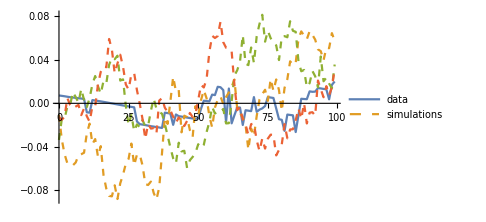
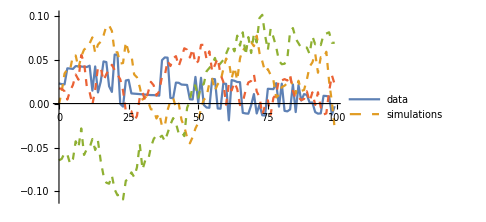

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.5819,5041.86},{17.5221,4801.94},{17.54,4561.91},{17.5578,4321.89},{17.58,4081.86},{17.606,3841.83},{17.5267,3601.93},{17.5523,3361.9},{17.5766,3121.87},{17.6109,2881.83},{17.65,2641.78},{17.5368,2401.93}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

5041.86

17.5819

{5041.86,4801.94,4561.91,4321.89,4081.86,3841.83,3601.93,3361.9,3121.87,2881.83,2641.78,2401.93}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 4.82684 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 4.82693 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 710738 Kb

Memory Used: 4.14924 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,0,0,0,0,0,0,0,9}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.009}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

12

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.00069

1

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

12

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.01447,b→-0.798932,c→-0.0588442,d→0.020611,T_1→0.521327,tc→1.00069,m→0.4,ω→5.6,RSS→4.13774,ℛerror→0.00171052,ℛσ→0.0413072,LL→7620.77,ρ→0.966054,σ→-0.0106692,μ→-2.45702×10^-17,index→12}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

12

{a→1.01447,b→-0.798932,c→-0.0588442,d→0.020611,T_1→0.521327,tc→1.00069,m→0.4,ω→5.6,RSS→4.13774,ℛerror→0.00171052,ℛσ→0.0413072,LL→7620.77,ρ→0.966054,σ→-0.0106692,μ→-2.45702×10^-17}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.4

5.6

1.00069

7620.77

```mathematica
t1=Subscript[T, 1]/.fit
```

0.521327

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

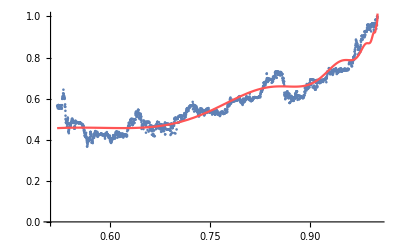

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.01447,b→-0.798932,c→-0.0588442,d→0.020611,T_1→0.521327,tc→1.00069,m→0.4,ω→5.6,RSS→4.13774,ℛerror→0.00171052,ℛσ→0.0413072,LL→7620.77,ρ→0.966054,σ→-0.0106692,μ→-2.45702×10^-17}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.966054,σ→-0.0106692,μ→-2.45702×10^-17}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

LessEqual::nord: Invalid comparison with 1.54925×10^13-5.57132×10^13 ⅈ attempted.

Less::nord: Invalid comparison with 1.54925×10^13-5.57132×10^13 ⅈ attempted.

LessEqual::nord: Invalid comparison with 1.54925×10^13-5.57132×10^13 ⅈ attempted.

Less::nord: Invalid comparison with 1.54925×10^13-5.57132×10^13 ⅈ attempted.

1.54925×10^13-5.57132×10^13 ⅈ

{0.999693,1.00069}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92006

{0.999693,1.00069,1.00388}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.00059

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Tue 27 Jan 2026 19:26:42

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Wed 28 Jan 2026 00:30:21

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Wed 28 Jan 2026 16:36:42

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Wed 28 Jan 2026 00:30:21

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Wed 28 Jan 2026 00:30:21

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Wed 28 Jan 2026 00:30:21

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Tue 1 Jul 2025 00:00:00 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.0473934 | Thu 10 Jul 2025 23:51:28 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.0947867 | Sun 20 Jul 2025 23:42:56 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.14218 | Wed 30 Jul 2025 23:34:24 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.189573 | Sat 9 Aug 2025 23:25:52 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.236967 | Tue 19 Aug 2025 23:17:20 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.28436 | Fri 29 Aug 2025 23:08:48 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.331754 | Mon 8 Sep 2025 23:00:17 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.379147 | Thu 18 Sep 2025 22:51:45 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.42654 | Sun 28 Sep 2025 22:43:13 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.473934 | Wed 8 Oct 2025 22:34:41 | tc→1.00069 | Wed 28 Jan 2026 00:30:21
T_1→0.521327 | Sat 18 Oct 2025 22:26:09 | tc→1.00069 | Wed 28 Jan 2026 00:30:21

```mathematica
(* Compute price at the low leg of the best Tc: *)
bestP=bestLppls[bestTc-epsilon,bestTc]
```

0.99352

```mathematica
lowCIP=bestLppls[lowCItc,bestTc]
```

0.96092

```mathematica
lastScaledP=bubbleBest[[-1]][[2]]
```

0.992607

```mathematica
lastPriceDate
```

2026-01-29

```mathematica
(* Closing price at `lastPriceDate` date: *)
latestPrice=hourlyPrices[[-1]][[2]]
```

5511.77

```mathematica
(* Plot predicted price evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVP[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestPrice/Exp[lastScaledP]]]},{i,min, max,1/8}]
```

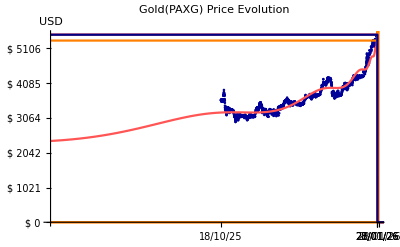

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"Gold(PAXG) Price Evolution",PlotRange->{{0,maxTc},{0,Exp[bestP]}}, Ticks->{ticksH,ticksVP},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestP+1],UnitStep[ti-highCItc]Exp[bestP+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIP],UnitStep[bestTc-ti]Exp[bestP],UnitStep[lastScaledTc-ti]Exp[lastScaledP]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/Gold(PAXG)_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/Gold(PAXG)_PricePrediction-2026-01-29.png

```mathematica
pToPrice[p_]:= Exp[p] latestPrice/Exp[lastScaledP]
```

```mathematica
(* Check: *)
lastPrice=pToPrice[lastScaledP]
```

5511.77

```mathematica
lowCIPrice=pToPrice[lowCIP]
```

5339.85

```mathematica
bestPrice=pToPrice[bestP]
```

5516.81